```mathematica
notebDir=("FileName"/.NotebookInformation[SelectedNotebook[]])[[1]]//ToFileName
```

/Users/malchiodi/Documents/Ricerca/shadowed-svm/

```mathematica
shadowedSvm[x_,y_,xShad_,c_]:=Block[{notebDir,stdin,i,k,retCode,m,mShad,n,stream},
m=Length[x];
mShad=Length[xShad];
n=Length[x[[1]]];
notebDir=("FileName"/.NotebookInformation[SelectedNotebook[]])[[1]]//ToFileName;
SetDirectory[notebDir];
stdin="param m integer > 0 default ";
stdin=stdin<>ToString[m] ;
stdin=stdin<>"; # number of labeled sample points\n";
stdin=stdin<>"param ms integer > 0 default ";
stdin=stdin<>ToString[mShad] ;
stdin=stdin<>"; # number of shadowed sample points\n";
stdin=stdin<>"param n integer > 0 default ";
stdin=stdin<>ToString[n];
stdin=stdin<>"; # sample space dimension\n\n";
stdin=stdin<>"param C integer > 0 default ";
stdin=stdin<>ToString[c];
stdin=stdin<>";\n\n";
stdin=stdin<>"param x {1..m,1..n}; # labeled sample points\n";
stdin=stdin<>"param xs {1..ms,1..n}; # shadowed sample points\n";
stdin=stdin<>"param y {1..m}; # sample labels\n";
stdin=stdin<>"param dot{i in 1..m,j in 1..m}:=sum{k in 1..n}x[i,k]*x[j,k];\n";
stdin=stdin<>"param dots{i in 1..ms,j in 1..ms}:=sum{k in 1..n}xs[i,k]*xs[j,k];\n";stdin=stdin<>"param dotmix{i in 1..m,j in 1..ms}:=sum{k in 1..n}x[i,k]*xs[j,k];\n\n";
stdin=stdin<>"var alpha{1..m}>=0 <=C;\n";
stdin=stdin<>"var gamma{1..ms}>=0;\n";
stdin=stdin<>"var delta{1..ms}>=0;\n\n";
stdin=stdin<>"maximize quadratic_form:\n";
stdin=stdin<>"sum{i in 1..m} alpha[i]\n";
stdin=stdin<>"-1/2*sum{i in 1..m,j in 1..m}alpha[i]*alpha[j]*y[i]*y[j]*dot[i,j]\n";
stdin=stdin<>"-1/2*sum{i in 1..ms,j in 1..ms}(gamma[i]-delta[i])*(gamma[j]-delta[j])*dots[i,j]\n";
stdin=stdin<>"-sum{i in 1..m,j in 1..ms}alpha[i]*y[i]*(gamma[j]-delta[j])*dotmix[i,j];\n\n";
stdin=stdin<>"subject to linear_constraint:\n";
stdin=stdin<>"sum{i in 1..m} alpha[i]*y[i] + sum{j in 1..ms}(gamma[j]-delta[j]) = 0;\n\n";
stdin=stdin<>"subject to gamma_delta_constraint:\n";
stdin=stdin<>"sum{j in 1..ms}(gamma[j]+delta[j]) <= 1;\n\n";

stdin=stdin<>"data;\n\n";
stdin=stdin<>"param\tx:\t";
For[k=1,k≤n,k++,
stdin=stdin<>ToString[k]<>"\t";
];
stdin=stdin<>":=\n";
For[i=1,i≤m,i++,
stdin=stdin<>ToString[i]<>"\t";
For[k=1,k≤n,k++,
stdin=stdin<>ToString[x[[i]][[k]]]<>"\t";
];
stdin=stdin<>If[i==m,";\n\n","\n"];
];

stdin=stdin<>"param\txs:\t";
For[k=1,k≤n,k++,
stdin=stdin<>ToString[k]<>"\t";
];
stdin=stdin<>":=\n";
For[i=1,i≤mShad,i++,
stdin=stdin<>ToString[i]<>"\t";
For[k=1,k≤n,k++,
stdin=stdin<>ToString[xShad[[i]][[k]]]<>"\t";
];
stdin=stdin<>If[i==mShad,";\n\n","\n"];
];

stdin=stdin<>"param y :=\n";
For[i=1,i≤m,i++,
stdin=stdin<>ToString[i]<>"\t"<>ToString[y[[i]]];
stdin=stdin<>If[i==m,";\n\n","\n"];
];


stdin=stdin<>"option solver snopt;\n\n";
stdin=stdin<>"solve;\n\n";
stdin=stdin<>"printf: \"{{\";\n";
stdin=stdin<>"printf {i in 1..m-1}:\"%f,\",alpha[i];\n";
stdin=stdin<>"printf: \"%f},{\",alpha[m];\n";
stdin=stdin<>"printf {i in 1..ms-1}:\"%f,\",gamma[i];\n";
stdin=stdin<>"printf: \"%f},{\",gamma[ms];\n";
stdin=stdin<>"printf {i in 1..ms-1}:\"%f,\",delta[i];\n";
stdin=stdin<>"printf: \"%f}}\\n\",delta[ms];\n";

stream=OpenWrite["temp-ampl.mod"];
WriteString[stream,stdin];
Close[stream];
If[$OperatingSystem=="MacOSX",
retCode=Run["export PATH=.:$PATH; ampl < temp-ampl.mod > temp-ampl-result"],
retCode=Run["set PATH=.;$PATH & ampl < temp-ampl.mod > temp-ampl-result"]
];
If[retCode≠0,Return[$Failed]];
Return[ReadList["temp-ampl-result",Record][[-1]]//ToExpression];

]
```

```mathematica
standardSvm[x_,y_,c_]:=Block[{stdin,i,k,retCode,m,mShad,n,stream},
m=Length[x];
mShad=Length[xShad];
n=Length[x[[1]]];
SetDirectory[notebDir];
stdin="param m integer > 0 default ";
stdin=stdin<>ToString[m] ;
stdin=stdin<>"; # number of labeled sample points\n";
stdin=stdin<>"param n integer > 0 default ";
stdin=stdin<>ToString[n];
stdin=stdin<>"; # sample space dimension\n\n";
stdin=stdin<>"param C integer > 0 default ";
stdin=stdin<>ToString[c];
stdin=stdin<>";\n\n";
stdin=stdin<>"param x {1..m,1..n}; # labeled sample points\n";
stdin=stdin<>"param y {1..m}; # sample labels\n";
stdin=stdin<>"param dot{i in 1..m,j in 1..m}:=sum{k in 1..n}x[i,k]*x[j,k];\n";
stdin=stdin<>"var alpha{1..m}>=0 <=C;\n";
stdin=stdin<>"maximize quadratic_form:\n";
stdin=stdin<>"sum{i in 1..m} alpha[i]\n";
stdin=stdin<>"-1/2*sum{i in 1..m,j in 1..m}alpha[i]*alpha[j]*y[i]*y[j]*dot[i,j];\n";
stdin=stdin<>"subject to linear_constraint:\n";
stdin=stdin<>"sum{i in 1..m} alpha[i]*y[i] = 0;\n\n";


stdin=stdin<>"data;\n\n";
stdin=stdin<>"param\tx:\t";
For[k=1,k≤n,k++,
stdin=stdin<>ToString[k]<>"\t";
];
stdin=stdin<>":=\n";
For[i=1,i≤m,i++,
stdin=stdin<>ToString[i]<>"\t";
For[k=1,k≤n,k++,
stdin=stdin<>ToString[x[[i]][[k]]]<>"\t";
];
stdin=stdin<>If[i==m,";\n\n","\n"];
];


stdin=stdin<>"param y :=\n";
For[i=1,i≤m,i++,
stdin=stdin<>ToString[i]<>"\t"<>ToString[y[[i]]];
stdin=stdin<>If[i==m,";\n\n","\n"];
];


stdin=stdin<>"option solver snopt;\n\n";
stdin=stdin<>"solve;\n\n";
stdin=stdin<>"printf: \"{\";\n";
stdin=stdin<>"printf {i in 1..m-1}:\"%f,\",alpha[i];\n";
stdin=stdin<>"printf: \"%f}\\n\",alpha[m];\n";


stream=OpenWrite["./temp-ampl.mod"];
WriteString[stream,stdin];
Close[stream];
retCode=Run["export PATH=.:$PATH;./ampl < ./temp-ampl.mod > ./temp-ampl-result"];
If[retCode≠0,Return[$Failed]];
Return[ReadList["./temp-ampl-result",Record][[-1]]//ToExpression];

]
```

```mathematica
(*
 GENERATE_TWO_MOONS
INPUTS:% r:radius of 2 moons
w:width of the 2 moons
d:distance between the two moons
N:number of samples to generate in each moon*
* OUTPUTS:% X:2N X 2 matrix
* Y:2N X 1 vector--+1 for top moon-1 for bottom moon
* Xt:uniformly spaced points on a grid
*
* Vikas Sindhwani (vikass@cs.uchicago.edu)
*)
generateTwoMoons[r_,w_,d_,n_]:=Module[{R,rr,theta,Xup,Xdw,delX,delY},
rr=r+w/2;
(* randomly pick radial coordinate between r-w and r *)
R=(rr-w)Table[1,{n}]+RandomReal[{0,1},n]w;
theta=RandomReal[{0,1},n]*Pi;
Xup=Transpose[{R Cos[theta], R Sin[theta]}];

(* bottom moon *)

(* randomly pick radial coordinate between r-w and r *)
R=(rr-w)Table[1,{n}]+RandomReal[{0,1},n]w;

(* randomly pick the angular coordinate *)
theta=Pi+RandomReal[{0,1},n]*Pi;

(* move x coordinate by y coordinate down by d *)
delX=rr-(w/2);
delY=-d;
Xdw=Transpose[{R Cos[theta]+delX, R Sin[theta]+delY}];

Return[{Xup,Xdw}];
]
```

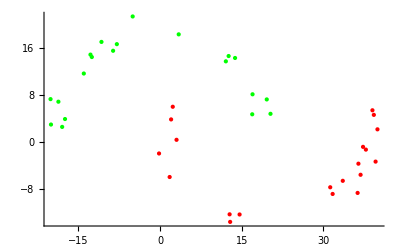

```mathematica
r=20;
w=5;
d=-6;
n=20;
moons=generateTwoMoons[r,w,d,n];
Show[ListPlot[moons[[1]],PlotStyle->Green],ListPlot[moons[[2]],PlotStyle->Red]]
```

```mathematica
r=20;
w=5;
d=-6;
m=4;

moons=generateTwoMoons[r,w,d,n];
Show[ListPlot[moons[[1]],PlotStyle->Green],ListPlot[moons[[2]],PlotStyle->Red]]

m=2;
x={{20, 4},{0, 4}};
y={1,-1};

mShad=2n;
xShad=Join@@moons;
```

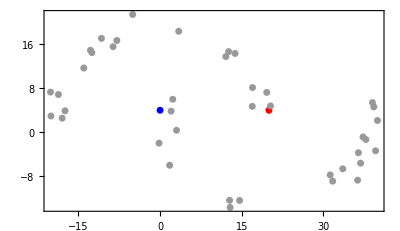

```mathematica
grPoints=Join[Table[{AbsolutePointSize[5],If[y[[i]]==1,RGBColor[1,0,0],RGBColor[0,0,1]],Point[x[[i]]]},{i,m}],
Table[{AbsolutePointSize[5],GrayLevel[0.6],Point[xShad[[i]]]},{i,mShad}]
]//Graphics;
Show[grPoints,Frame->True,AspectRatio->Automatic]
```

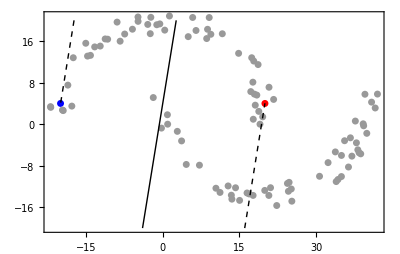

```mathematica
c=1000;
{alphas,gammas,deltas}=shadowedSvm[x,y,xShad,c];
w=alphas.(x y)+(gammas-deltas).xShad;
bs=y[[#]]-w.x[[#]]&/@Flatten[Position[alphas,a_/;0<a<c]];
b=Mean[bs];
epss=Join[-w.xShad[[#]]-b&/@Flatten[Position[gammas,g_/;g>0]],w.xShad[[#]]+b&/@Flatten[Position[deltas,d_/;d>0]]];
eps=Mean[epss];
grHyp=ContourPlot[w.{xx,yy}+b,{xx,-20,20},{yy,-20,20},ContourShading->False,Contours->{-1,-eps,0,eps,1},ContourStyle->{Gray,Dashing[{.01}],Black,Dashing[{.01}],Gray}];

Show[grPoints,grHyp,Frame->True,AspectRatio->Automatic]
```

```mathematica
eps
```

2.08661

## Rifacciamolo con kernel

```mathematica
shadowedKernelizedSvm[x_,y_,xShad_,c_,sigma_]:=Block[{stdin,i,k,retCode,m,mShad,n,stream},
m=Length[x];
mShad=Length[xShad];
n=Length[x[[1]]];
SetDirectory[notebDir];
stdin="param sigma > 0 default ";
stdin=stdin<>ToString[sigma] ;
stdin=stdin<>"; # polynomial kernel degree\n";
stdin=stdin<>"param m integer > 0 default ";
stdin=stdin<>ToString[m] ;
stdin=stdin<>"; # number of labeled sample points\n";
stdin=stdin<>"param ms integer > 0 default ";
stdin=stdin<>ToString[mShad] ;
stdin=stdin<>"; # number of shadowed sample points\n";
stdin=stdin<>"param n integer > 0 default ";
stdin=stdin<>ToString[n];
stdin=stdin<>"; # sample space dimension\n\n";
stdin=stdin<>"param C > 0 default ";
stdin=stdin<>ToString[c];
stdin=stdin<>";\n\n";
stdin=stdin<>"param x {1..m,1..n}; # labeled sample points\n";
stdin=stdin<>"param xs {1..ms,1..n}; # shadowed sample points\n";
stdin=stdin<>"param y {1..m}; # sample labels\n";
stdin=stdin<>"param dot{i in 1..m,j in 1..m}:=exp(-1*sum{k in 1..n}((x[i,k]-x[j,k])*(x[i,k]-x[j,k]))/(2*sigma*sigma));\n\n";
stdin=stdin<>"param dots{i in 1..ms,j in 1..ms}:=exp(-1*sum{k in 1..n}((xs[i,k]-xs[j,k])*(xs[i,k]-xs[j,k]))/(2*sigma*sigma));\n\n";
stdin=stdin<>"param dotmix{i in 1..m,j in 1..ms}:=exp(-1*sum{k in 1..n}((x[i,k]-xs[j,k])*(x[i,k]-xs[j,k]))/(2*sigma*sigma));\n\n";
stdin=stdin<>"var alpha{1..m}>=0 <=C;\n";
stdin=stdin<>"var gamma{1..ms}>=0;\n";
stdin=stdin<>"var delta{1..ms}>=0;\n\n";
stdin=stdin<>"maximize quadratic_form:\n";
stdin=stdin<>"sum{i in 1..m} alpha[i]\n";
stdin=stdin<>"-1/2*sum{i in 1..m,j in 1..m}alpha[i]*alpha[j]*y[i]*y[j]*dot[i,j]\n";
stdin=stdin<>"-1/2*sum{i in 1..ms,j in 1..ms}(gamma[i]-delta[i])*(gamma[j]-delta[j])*dots[i,j]\n";
stdin=stdin<>"-sum{i in 1..m,j in 1..ms}alpha[i]*y[i]*(gamma[j]-delta[j])*dotmix[i,j];\n\n";
stdin=stdin<>"subject to linear_constraint:\n";
stdin=stdin<>"sum{i in 1..m} alpha[i]*y[i] + sum{j in 1..ms}(gamma[j]-delta[j]) = 0;\n\n";
stdin=stdin<>"subject to gamma_delta_constraint:\n";
stdin=stdin<>"sum{j in 1..ms}(gamma[j]+delta[j]) <= 1;\n\n";

stdin=stdin<>"data;\n\n";
stdin=stdin<>"param\tx:\t";
For[k=1,k≤n,k++,
stdin=stdin<>ToString[k]<>"\t";
];
stdin=stdin<>":=\n";
For[i=1,i≤m,i++,
stdin=stdin<>ToString[i]<>"\t";
For[k=1,k≤n,k++,
stdin=stdin<>ToString[x[[i]][[k]]]<>"\t";
];
stdin=stdin<>If[i==m,";\n\n","\n"];
];

stdin=stdin<>"param\txs:\t";
For[k=1,k≤n,k++,
stdin=stdin<>ToString[k]<>"\t";
];
stdin=stdin<>":=\n";
For[i=1,i≤mShad,i++,
stdin=stdin<>ToString[i]<>"\t";
For[k=1,k≤n,k++,
stdin=stdin<>ToString[xShad[[i]][[k]]]<>"\t";
];
stdin=stdin<>If[i==mShad,";\n\n","\n"];
];

stdin=stdin<>"param y :=\n";
For[i=1,i≤m,i++,
stdin=stdin<>ToString[i]<>"\t"<>ToString[y[[i]]];
stdin=stdin<>If[i==m,";\n\n","\n"];
];


stdin=stdin<>"option solver snopt;\n\n";
stdin=stdin<>"solve;\n\n";
stdin=stdin<>"printf: \"{{\";\n";
stdin=stdin<>"printf {i in 1..m-1}:\"%f,\",alpha[i];\n";
stdin=stdin<>"printf: \"%f},{\",alpha[m];\n";
stdin=stdin<>"printf {i in 1..ms-1}:\"%f,\",gamma[i];\n";
stdin=stdin<>"printf: \"%f},{\",gamma[ms];\n";
stdin=stdin<>"printf {i in 1..ms-1}:\"%f,\",delta[i];\n";
stdin=stdin<>"printf: \"%f}}\\n\",delta[ms];\n";

stream=OpenWrite["./temp-ampl.mod"];
WriteString[stream,stdin];
Close[stream];
retCode=Run["export PATH=.:$PATH;./ampl < ./temp-ampl.mod > ./temp-ampl-result"];
If[retCode≠0,Return[$Failed]];
Return[ReadList["./temp-ampl-result",Record][[-1]]//ToExpression];

]
```

```mathematica
standardKernelizedSvm[x_,y_,c_,p_]:=Block[{stdin,i,k,retCode,m,mShad,n,stream},
m=Length[x];
mShad=Length[xShad];
n=Length[x[[1]]];
SetDirectory[notebDir];
stdin="param p integer > 0 default ";
stdin=stdin<>ToString[p] ;
stdin=stdin<>"; # polynomial kernel degree\n";
stdin=stdin<>"param m integer > 0 default ";
stdin=stdin<>ToString[m] ;
stdin=stdin<>"; # number of labeled sample points\n";
stdin=stdin<>"param n integer > 0 default ";
stdin=stdin<>ToString[n];
stdin=stdin<>"; # sample space dimension\n\n";
stdin=stdin<>"param C integer > 0 default ";
stdin=stdin<>ToString[c];
stdin=stdin<>";\n\n";
stdin=stdin<>"param x {1..m,1..n}; # labeled sample points\n";
stdin=stdin<>"param y {1..m}; # sample labels\n";
stdin=stdin<>"param dot{i in 1..m,j in 1..m}:=(1+sum{k in 1..n}x[i,k]*x[j,k])^p;\n";
stdin=stdin<>"var alpha{1..m}>=0 <=C;\n";
stdin=stdin<>"maximize quadratic_form:\n";
stdin=stdin<>"sum{i in 1..m} alpha[i]\n";
stdin=stdin<>"-1/2*sum{i in 1..m,j in 1..m}alpha[i]*alpha[j]*y[i]*y[j]*dot[i,j];\n";
stdin=stdin<>"subject to linear_constraint:\n";
stdin=stdin<>"sum{i in 1..m} alpha[i]*y[i] = 0;\n\n";


stdin=stdin<>"data;\n\n";
stdin=stdin<>"param\tx:\t";
For[k=1,k≤n,k++,
stdin=stdin<>ToString[k]<>"\t";
];
stdin=stdin<>":=\n";
For[i=1,i≤m,i++,
stdin=stdin<>ToString[i]<>"\t";
For[k=1,k≤n,k++,
stdin=stdin<>ToString[x[[i]][[k]]]<>"\t";
];
stdin=stdin<>If[i==m,";\n\n","\n"];
];


stdin=stdin<>"param y :=\n";
For[i=1,i≤m,i++,
stdin=stdin<>ToString[i]<>"\t"<>ToString[y[[i]]];
stdin=stdin<>If[i==m,";\n\n","\n"];
];


stdin=stdin<>"option solver snopt;\n\n";
stdin=stdin<>"solve;\n\n";
stdin=stdin<>"printf: \"{\";\n";
stdin=stdin<>"printf {i in 1..m-1}:\"%f,\",alpha[i];\n";
stdin=stdin<>"printf: \"%f}\\n\",alpha[m];\n";


stream=OpenWrite["./temp-ampl.mod"];
WriteString[stream,stdin];
Close[stream];
retCode=Run["export PATH=.:$PATH;./ampl < ./temp-ampl.mod > ./temp-ampl-result"];
If[retCode≠0,Return[$Failed]];
Return[ReadList["./temp-ampl-result",Record][[-1]]//ToExpression];

]
```

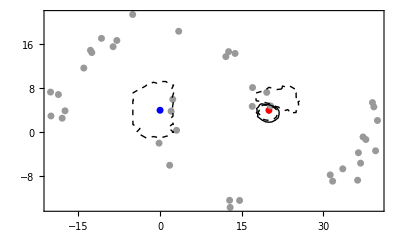

```mathematica
c=10;
sigma=0.9238935;
{alphas,gammas,deltas}=shadowedKernelizedSvm[x,y,xShad,c,sigma];
k[x1_,x2_]:=Exp[-1*Norm[x1-x2]^2/(2*sigma*sigma)];
bs=Table[y[[i]]-alphas.(y(k[#,x[[i]]]&/@x))-(gammas-deltas).(k[#,x[[i]]]&/@xShad),{i,Flatten[Position[alphas,a_/;0<a<c]]}];
b=Mean[bs];
epss=Join[Table[(-alphas.(y(k[#,xShad[[i]]]&/@x))-(gammas-deltas).(k[#,xShad[[i]]]&/@xShad)-b),{i,Flatten[Position[gammas,g_/;g>0]]}],Table[(alphas.(y(k[#,xShad[[i]]]&/@x))+(gammas-deltas).(k[#,xShad[[i]]]&/@xShad)+b),{i,Flatten[Position[deltas,d_/;d>0]]}]];
eps=Mean[epss];
grHyp=ContourPlot[alphas.(y(k[#,{xx,yy}]&/@x))+(gammas-deltas).(k[#,{xx,yy}]&/@xShad)+b,{xx,-25,45},{yy,-20,20},ContourShading->False,Contours->{-1,-eps,0,eps,1},ContourStyle->{Gray,Dashing[{.01}],Black,Dashing[{.01}],Gray}];
grSep1=ContourPlot[alphas.(y(k[#,{xx,yy}]&/@x))+(gammas-deltas).(k[#,{xx,yy}]&/@xShad)+b,{xx,-25,45},{yy,-20,20},ContourShading->False,Contours->{0},ContourStyle->{Black}];
Show[grPoints,grHyp,Frame->True,AspectRatio->Automatic]
```

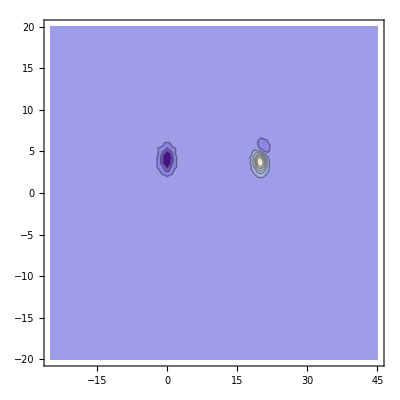

```mathematica
ContourPlot[alphas.(y(k[#,{xx,yy}]&/@x))+(gammas-deltas).(k[#,{xx,yy}]&/@xShad)+b,{xx,-25,45},{yy,-20,20}]
```

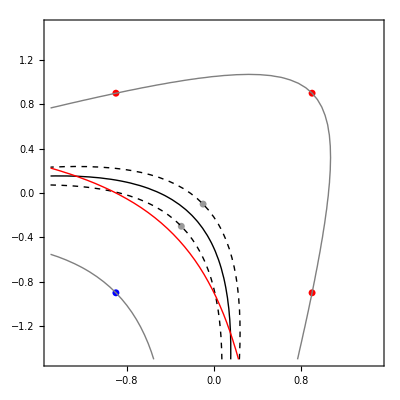

```mathematica
alphas=standardKernelizedSvm[x,y,c,p];

bs=Table[y[[i]]-alphas.(y(k[#,x[[i]]]&/@x)),{i,Flatten[Position[alphas,a_/;0<a<c]]}];
b=Mean[bs];

grSVMHyp=ContourPlot[alphas.(y(k[#,{xx,yy}]&/@x))+b,{xx,-1.5,1.5},{yy,-1.5,1.5},ContourShading->False,Contours->{0},ContourStyle->{Red}];
Show[grPoints,grHyp,grSVMHyp,Frame->True,AspectRatio->Automatic,PlotRange->{{-1.5,1.5},{-1.5,1.5}}]
```

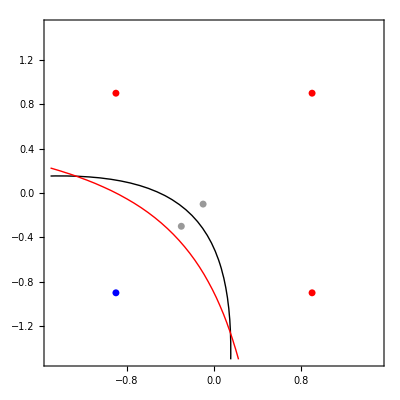

```mathematica
Show[grSep1,grSVMHyp,grPoints,PlotRange->{{-1.5,1.5},{-1.5,1.5}}]
```

```mathematica
eps
```

0.122807

```mathematica
m=4;
x={{-.9,-.9},{.9,-.9},{-.9,.9},{.9,.9}};
y={-1,1,1,1};
mShad=3;
xShad={{0.3,0.3},{-.5,-.5},{.8,-.8}};
```

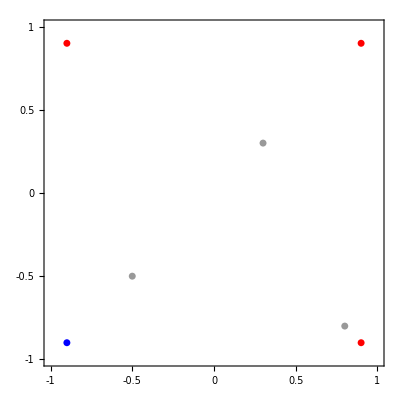

```mathematica
grPoints=Join[Table[{AbsolutePointSize[5],If[y[[i]]==1,RGBColor[1,0,0],RGBColor[0,0,1]],Point[x[[i]]]},{i,m}],
Table[{AbsolutePointSize[5],GrayLevel[0.6],Point[xShad[[i]]]},{i,mShad}]
]//Graphics;
Show[grPoints,Frame->True,AspectRatio->Automatic,PlotRange->{{-1,1},{-1,1}},FrameTicks->{{-1,-0.5,0,0.5,1},{-1,-0.5,0,0.5,1},None,None}]
```

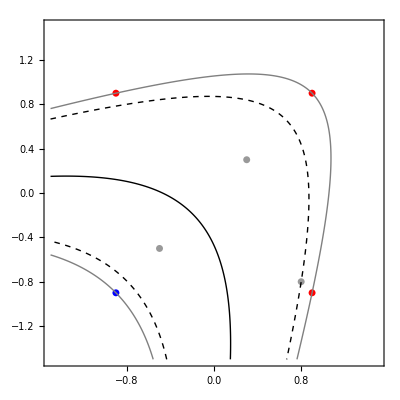

```mathematica
c=1000;
p=2;
{alphas,gammas,deltas}=shadowedKernelizedSvm[x,y,xShad,c,p];
k[x1_,x2_]:=(1+x1.x2)^p;
bs=Table[y[[i]]-alphas.(y(k[#,x[[i]]]&/@x))-(gammas-deltas).(k[#,x[[i]]]&/@xShad),{i,Flatten[Position[alphas,a_/;0<a<c]]}];
b=Mean[bs];
epss=Join[Table[(-alphas.(y(k[#,xShad[[i]]]&/@x))-(gammas-deltas).(k[#,xShad[[i]]]&/@xShad)-b),{i,Flatten[Position[gammas,g_/;g>0]]}],Table[(alphas.(y(k[#,xShad[[i]]]&/@x))+(gammas-deltas).(k[#,xShad[[i]]]&/@xShad)+b),{i,Flatten[Position[deltas,d_/;d>0]]}]];
eps=Mean[epss];
grHyp=ContourPlot[alphas.(y(k[#,{xx,yy}]&/@x))+(gammas-deltas).(k[#,{xx,yy}]&/@xShad)+b,{xx,-1.5,1.5},{yy,-1.5,1.5},ContourShading->False,Contours->{-1,-eps,0,eps,1},ContourStyle->{Gray,Dashing[{.01}],Black,Dashing[{.01}],Gray},PlotPoints->100];
grSep2=ContourPlot[alphas.(y(k[#,{xx,yy}]&/@x))+(gammas-deltas).(k[#,{xx,yy}]&/@xShad)+b,{xx,-1.5,1.5},{yy,-1.5,1.5},ContourShading->False,Contours->{0},ContourStyle->{Black},PlotPoints->100];
Show[grPoints,grHyp,Frame->True,AspectRatio->Automatic,PlotRange->{{-1.5,1.5},{-1.5,1.5}}]
```

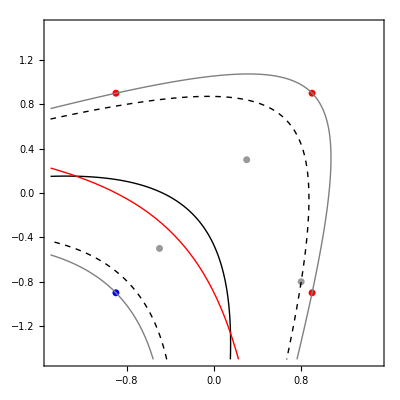

```mathematica
alphas=standardKernelizedSvm[x,y,c,p];

bs=Table[y[[i]]-alphas.(y(k[#,x[[i]]]&/@x)),{i,Flatten[Position[alphas,a_/;0<a<c]]}];
b=Mean[bs];

grSVMHyp=ContourPlot[alphas.(y(k[#,{xx,yy}]&/@x))+b,{xx,-1.5,1.5},{yy,-1.5,1.5},ContourShading->False,Contours->{0},ContourStyle->{Red}];
Show[grPoints,grHyp,grSVMHyp,Frame->True,AspectRatio->Automatic,PlotRange->{{-1.5,1.5},{-1.5,1.5}}]
```

```mathematica
eps
```

0.837262

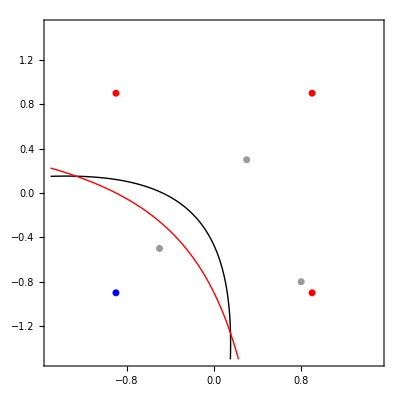

```mathematica
Show[grSep2,grSVMHyp,grPoints,PlotRange->{{-1.5,1.5},{-1.5,1.5}}]
```